```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,xcolor,bm,mhchem}","\\definecolor{darkgreen}{RGB}{0, 180, 0}"}];
```

```mathematica
HUMP[λ_,t_,U_]=({{-(2 t^2 λ)/U, 0, 0, (2 t^2 λ)/U}, {0, U-(2 t^2 λ)/U, (2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U}, {0, (2 t^2 λ)/U, U-(2 t^2 λ)/U, -(2 t √(-4 t^2+U^2) λ)/U}, {(2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U, -(2 t √(-4 t^2+U^2) λ)/U, -2 U (-1+λ)+(6 t^2 λ)/U}});
ϵUMP[λ_,t_,U_]=Eigenvalues[HUMP[λ,t,U]];
```

```mathematica
RadConv[t_,U_]:=
Sort[
Abs[λ]/.NSolve[
{
Det[HUMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]],D[Det[HUMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]], Ε]
},{Ε,λ}]
]//DeleteDuplicates
```

```mathematica
TabRadConv=With[{ΔU=1/100},Table[{U,RadConv[1,U]},{U,ΔU,8,ΔU}]];
```

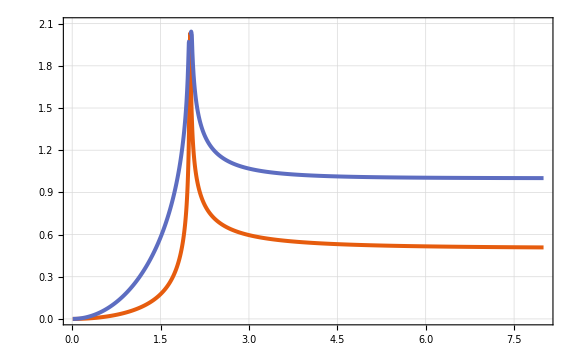

```mathematica
ListPlot[{
Table[{TabRadConv⟦k,1⟧,TabRadConv⟦k,2,2⟧},{k,Length[TabRadConv]}],
Table[{TabRadConv⟦k,1⟧,TabRadConv⟦k,2,3⟧},{k,Length[TabRadConv]}]
},Joined->True,InterpolationOrder->2,PlotTheme->"Scientific",
PlotRange->{All,{0,2.1}},PlotStyle->Thickness[0.005],
BaseStyle->20,ImageSize->Large,GridLines->Automatic,FrameLabel->{MaTeX["U/t",FontSize->20],MaTeX["r_c",FontSize->20]}]
```